```mathematica
ℏ = 1.054571596 10^-27;c=2.99792458 10^10;Subscript[m, e]=9.10938188 10^-28; Subscript[α, e]=7.297352533 10^-3;Subscript[Gm, e]= 1.16639 10^-5( 0.510998902 10^-3)^2;
Subscript[g, Ve]=1/2+2 (0.23);Subscript[g, Vμ]=-1/2+2( 0.23);Subscript[g, Ae]=1/2;Subscript[g, Aμ]=-1/2;Subscript[g, V]=√(Subscript[g, Ve]^2+2 Subscript[g, Vμ]^2);Subscript[g, A]=√(Subscript[g, Ae]^2+2 Subscript[g, Aμ]^2);
```

```mathematica
Subscript[λ, e]= ℏ/(Subscript[m, e] c);
Subscript[τ, e] =Subscript[λ, e]/c;
Subscript[E, e] = Subscript[m, e] c^2;
Subscript[Q, e] = Subscript[E, e]/(Subscript[λ, e]^3 Subscript[τ, e]) ;
 Subscript[N, e] = 1/(Subscript[λ, e]^3 Subscript[τ, e]);
```

```mathematica
RR00[x_]:=1+12.306728780393993/x^(1/2)+159.28494555577515/x^(3/2)+866.7067019290372/x^(5/2)+4511.652667090261/x^(7/2)+10960.54437176578/x^(9/2)+20170.404437273137/x^(11/2)+16575.589106915428/x^(13/2)+2991.9346396672163/x^(15/2);
Qnres[b_,y_,t_]:=(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] b((2 Subscript[α, e] b)/π )^(15/4) (((2*28*y)/(3*56*b))^2*1.009^6+1)^-3(t)^(3/2) Exp[-((2 Subscript[α, e] b)/(π (t)^2))^(1/2)] RR00[1/2((2 Subscript[α, e] b)/(π (t)^2))^(1/2)];
```

```mathematica
Qres[b_,y_,t_]:=(Subscript[Gm, e]^2*Subscript[Q, e]*(1-9 Exp[-1]/4))/(9*2^(1/4)*π^(9/2))*(Subscript[g, V]^2+Subscript[g, A]^2)(b)^(17/4) √t Exp[(√(((2*28*y)/(3*56*b))^2*1.009^6+1))/t-(√(2 b))/t];
```

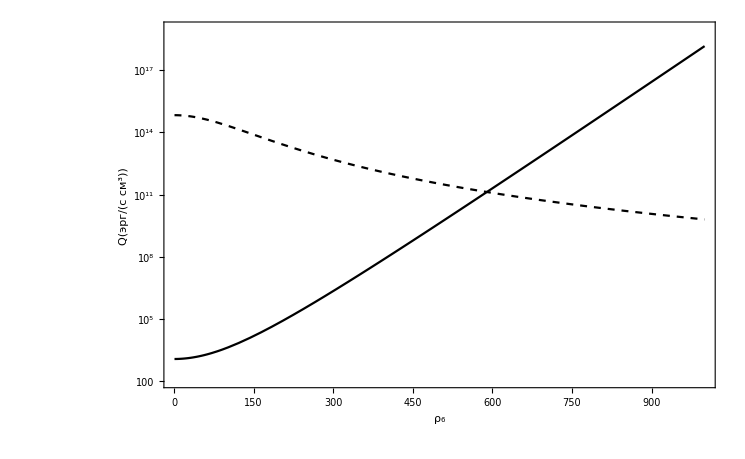

```mathematica
LogPlot[{Qnres[50,y,0.17],Qres[50,y,0.17]},{y,1,1000},PlotRange->{{1,1000},{100,10^19}},PlotStyle->{{Black,Dashed},Black},Frame->True,FrameLabel->{Subscript[ρ, 6],Q [эрг/(с*см^3)]},RotateLabel->False,LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```

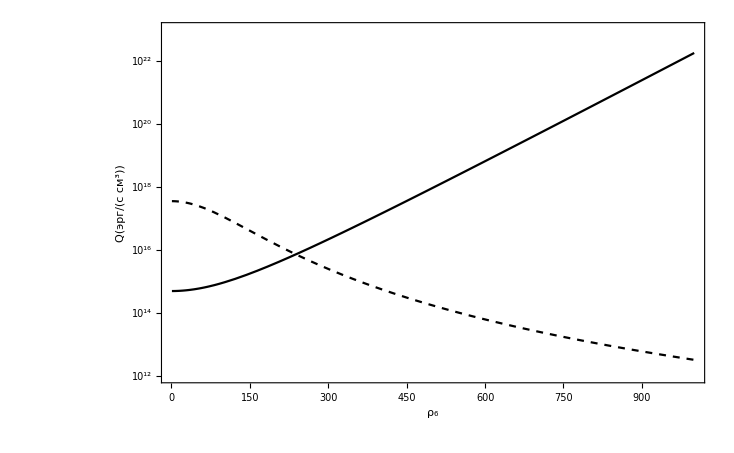

```mathematica
LogPlot[{Qnres[50,y,0.34],Qres[50,y,0.34]},{y,1,1000},PlotRange->{{1,1000},{10^12,10^23}},PlotStyle->{{Black,Dashed},Black},Frame->True,FrameLabel->{Subscript[ρ, 6],Q [эрг/(с*см^3)]},RotateLabel->False,LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```

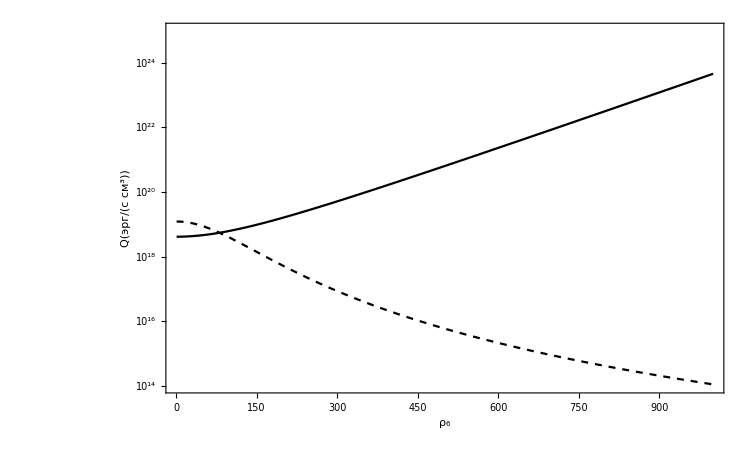

```mathematica
LogPlot[{Qnres[50,y,0.51],Qres[50,y,0.51]},{y,1,1000},PlotRange->{{1,1000},{10^14,10^25}},PlotStyle->{{Black,Dashed},Black},Frame->True,FrameLabel->{Subscript[ρ, 6],Q [эрг/(с*см^3)]},RotateLabel->False,LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```